# Zika vaccine MS results

```mathematica
Quit[]
```

## Setup

### Headers

```mathematica
If[$CommandLine[[2]]=="-wstp",ClusterRun=False,ClusterRun=True];
```

```mathematica
If[ClusterRun,SetDirectory["./"],SetDirectory[NotebookDirectory[]]];
```

```mathematica
Import["Zika vaccine model setup.m"]
```

## Figure 1 - Plot time series

### Setup

#### Read in data

```mathematica
SetDirectory[NotebookDirectory[]<>"/GeneratedResults/VaccineImpactTimeSeries"]
```

C:\Users\carbon\Dropbox\Code\Git\ZikaVaccineModel\GeneratedResults\VaccineImpactTimeSeries

```mathematica
vaccineTimeSeriesScenarios=Get["vaccineTimeSeriesScenarios.dat"];
```

#### Setup plots

```mathematica
Clear@plotFigure1
plotFigure1[data_,outcome_,legend_,cumulative_:False,yrange_:All,ysteps_:Automatic,xrange_:{0,3*52}]:=ListLinePlot[If[cumulative,#[outcome],Differences[#[outcome]]]&/@Values[data],
PlotRange->{xrange,yrange},PlotLegends->legend,
PlotStyle->{Directive[Black,Dashed],Black,Directive[Black,Dotted],Directive[Black,DotDashed],Directive[Black,Dashing]},
LabelStyle->Directive[Black,16],

Frame->{True,True,False,False},
FrameStyle->Black,
FrameLabel->{"Year","Infections"},
FrameTicks->{{If[ysteps==Automatic,Automatic,Range[yrange[[1]],yrange[[2]],ysteps]],None},{{#,#/52}&/@Range[52,52*3,52],None}},

ImageSize->{Automatic,200}
]
```

### Plot “best fit”

#### Plot all infections

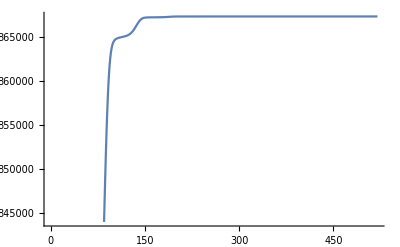

```mathematica
ListLinePlot@vaccineTimeSeriesScenarios["NoVaccination"]["allInfections"]
```

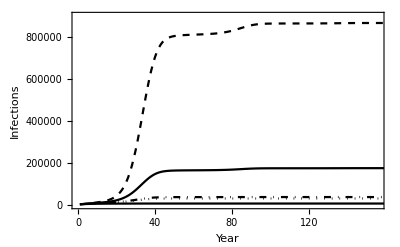

```mathematica
plotFigure1[vaccineTimeSeriesScenarios,"allInfections",None,True,{0,900000},300000]
```

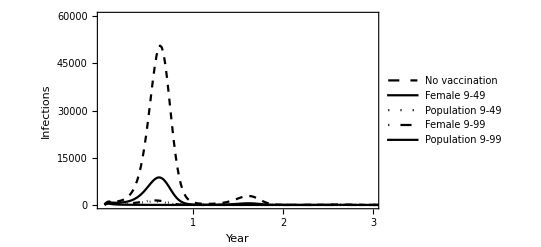

```mathematica
plotFigure1[vaccineTimeSeriesScenarios,"allInfections",{"No vaccination","Female 9-49","Population 9-49","Female 9-99","Population 9-99"},False,{0,60000},20000]
```

#### Plot prenatal infections infections

```mathematica
Keys@vaccineTimeSeriesScenarios
```

{NoVaccination,WHOfemale,WHOall,allfemale,allpopulation}

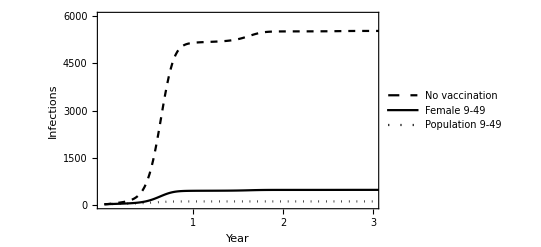

```mathematica
Show[
plotFigure1[vaccineTimeSeriesScenarios[[;;3]],"prenatalInfections",{"No vaccination","Female 9-49","Population 9-49","Female 9-99","Population 9-99"}[[;;3]],True,{0,6000},2000],
Graphics[Text[Style["A",Bold,16],{-10,100}]]
]
```

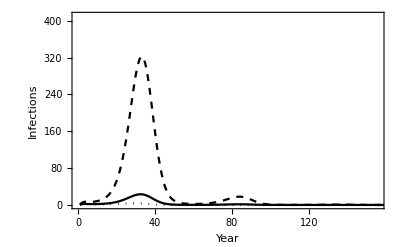

```mathematica
plotFigure1[vaccineTimeSeriesScenarios[[;;3]],"prenatalInfections",None,False,{0,410},100]
```